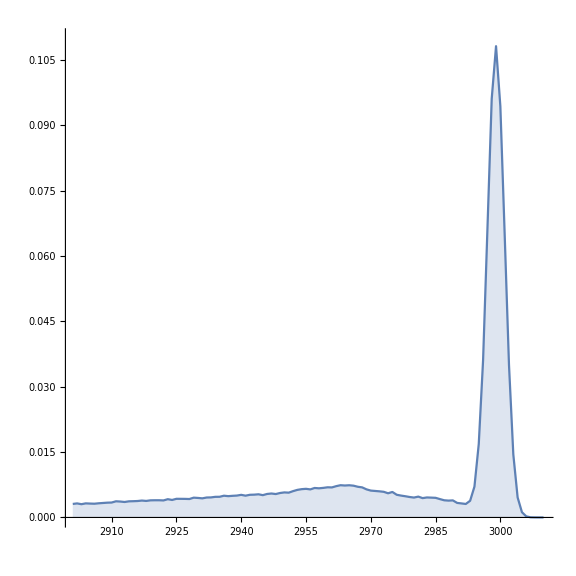

```mathematica
Clear[cy,sx,data,s,c];
Get["D:\\sx.dat"];
data=Table[{2900+i,s[[i]]},{i,1,110}];
p1=ListLinePlot[data,AspectRatio->1,ImageSize->Large,PlotRange->{0,0.11},Filling->Bottom,PlotStyle->Red]
```

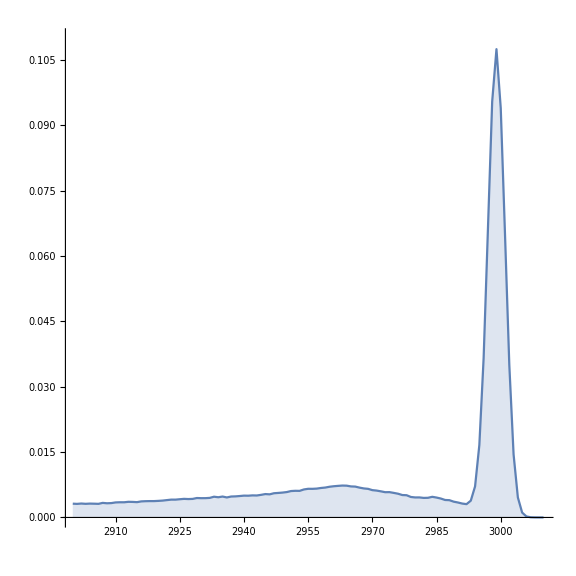

```mathematica
Clear[cy,sq,data,s,c];
Get["D:\\cy.dat"];
data=Table[{2900+i-1,c[[i]]},{i,1,111}];
p2=ListLinePlot[data,AspectRatio->1,ImageSize->Large,PlotRange->{0,0.11},Filling->Bottom]
```

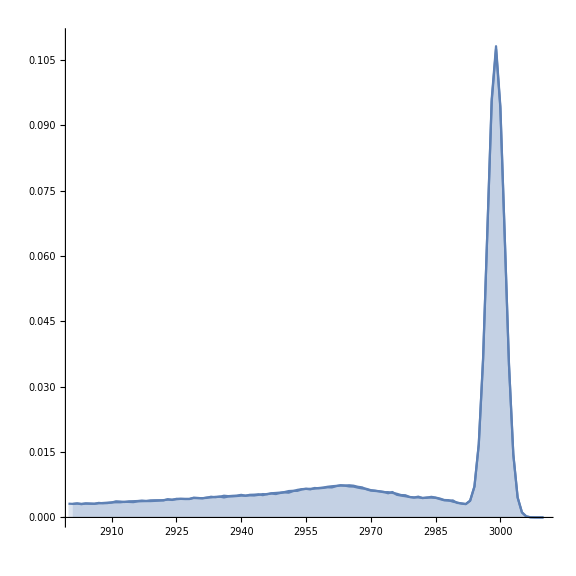

```mathematica
Show[p1,p2,PlotLegends->{"one","two"}]
```

```mathematica
Clear[cy,sq,data,s,c];
Get["D:\\cy.dat"];
data=Table[{2900+i-1,c[[i]]},{i,1,111}];
p3=ListLinePlot[data,AspectRatio->1,ImageSize->Large,PlotRange->{0,0.11},Filling->Bottom]
```

-Graphics-

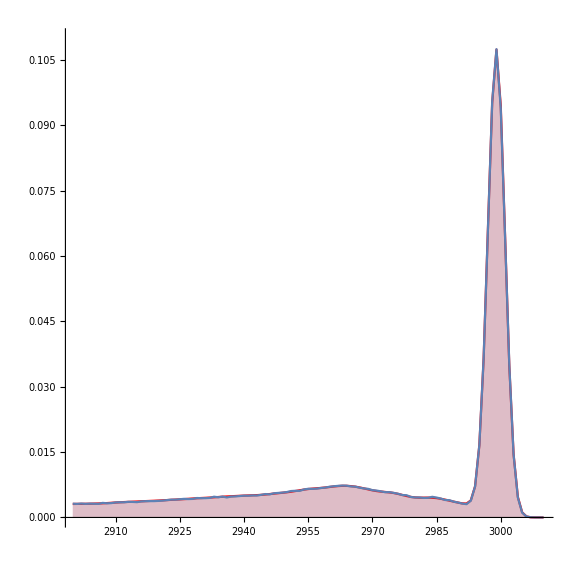

```mathematica
Show[p1,p3]
```